I studied several cases where the stress and instantaneous G are huge. I found that all the huge (and wrong) results are associated with false Voronoi Tessellation. I also found cellGPU sometimes gives false Tessellations and that might not necessarily leads to an obvious deviation from the right results. They might be due to the fail of triangulation_test, or suggest that some thresholds should be modified for the high temperatures. I tried to read through the relevant parts in cellGPU, but I’m not familiar with the GPU-type calculations, so I haven’t really figured it out. Hence, I include one snapshots with three false triangulations in the notebook, so maybe you can give me some insights of what might be wrong.

I run a batch of simulations with N=100, p=3.80, T=0.5. The simulations will stop once it detect a sigma larger than a threshold (I randomly choose 10 because it’s 2 order’s of magnitude larger than usual magnitude), and write the snapshot.
In each snapshot recorded, I loaded the d2Edgammadgamma, sigma, position, neighbors (defined by  cellGPUmm) for each cell, so that I can find out which cells are wrong and why.

## Analytical functions

```mathematica
(*Cross product for 2d vectors*)
Cross2d[r1_,r2_]:=r1[[1]]r2[[2]]-r1[[2]]r2[[1]]
(*The vertex position given the three adjecent cell positions*)
voro[ri_,rj_,rk_]:=Module[{rij,rjk,rik,cross,d,α,β,γ},
rij=ri-rj;
rjk=rj-rk;
rik=ri-rk;

cross=Cross2d[rij,rjk];
d=2*cross*cross;

α=(rjk.rjk)*(rij.rik)/d;
β=-(rik.rik)*(rij.rjk)/d;
γ=(rij.rij)*(rik.rjk)/d;

α*ri+β*rj+γ*rk
];
```

```mathematica
(*calculate perimetes and areas given the positions of all the vertices*)
peri[hv_List]:=Sum[Sqrt[(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]).(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]])],{i,1,Length[hv]}];

area[hv_List]:=Sum[0.5*Cross2d[hv[[i]],hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]],{i,1,Length[hv]}];
```

```mathematica
(*This is the 1st derivative of e w.r.t. h*)
dedhGeneral[hv_List,KA_,KP_,PA_,PP_]:=Module[{dedhx,dedhy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
dedhx=(-1. hiLasty+1. hiNexty) KA (a-PA)+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
dedhy=(-1. hiLastx+1. hiNextx) KA (PA-a)+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
{dedhx,dedhy}
]
```

```mathematica
(*This is the generalized function for de2dhidhj*)

de2dhihjxx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xx=2 ((-0.5 hiLasty+0.5 hiNexty)^2 KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLastx+hix)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNextx+hix)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2xx=2 ((-0.5 hiy+0.5 hjNexty) (-0.5 hiLasty+0.5 hjy) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[j==Length[hv],
de2xx=2 ((0.5 hiy-0.5 hjLasty) (0.5 hiNexty-0.5 hjy) KA+((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2xx=2 (-0.5 hiLasty+0.5 hiNexty) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xx
];
de2dhihjxy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xy=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2xy=2 (0.5 hix-0.5 hjNextx) (-0.5 hiLasty+0.5 hjy) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP- KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2xy=2 (-0.5 hix+0.5 hjLastx) (0.5 hiNexty-0.5 hjy) KA+2 ((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP+KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2xy=2 (-0.5 hiLasty+0.5 hiNexty) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xy
];
de2dhihjyx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yx=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2yx=2 (-0.5 hiy+0.5 hjNexty) (0.5 hiLastx-0.5 hjx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP+ KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2yx=2 (0.5 hiy-0.5 hjLasty) (-0.5 hiNextx+0.5 hjx) KA+2 ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) ((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) KP-KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2yx=2 (0.5 hiLastx-0.5 hiNextx) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yx
];
de2dhihjyy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yy=2 ((-0.5 hiLastx+0.5 hiNextx)^2 KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLasty+hiy)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNexty+hiy)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2yy=2 ((0.5 hix-0.5 hjNextx) (0.5 hiLastx-0.5 hjx) KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[j==Length[hv],
de2yy=2 ((-0.5 hix+0.5 hjLastx) (-0.5 hiNextx+0.5 hjx) KA+((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2yy=2 (0.5 hiLastx-0.5 hiNextx) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yy
];
de2dhdhGeneral[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{},
{{de2dhihjxx[hv,j,KA,KP,PA,PP],de2dhihjxy[hv,j,KA,KP,PA,PP]},{de2dhihjyx[hv,j,KA,KP,PA,PP],de2dhihjyy[hv,j,KA,KP,PA,PP]}}
]
```

```mathematica
(*These are the analytical forms for dhdgamma and d2hdgamma2*)
dhdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(r1x r1y (r2y-r3y)+r2y (r2x-r3x) r3y+r1y (-r2x r2y+r3x r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-2 r2x r2y r3x+r2y r3x^2-r2x^2 r3y-r2y^2 r3y+2 r2x r3x r3y+r2y r3y^2+r1x^2 (-r2y+r3y)+r1y^2 (-r2y+r3y)+2 r1x (r2x r2y+r1y (-r2x+r3x)-r3x r3y)+r1y (r2x^2+r2y^2-r3x^2-r3y^2))/(2 (-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y))}
];
d2hdgdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{((r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-r2y^2 r3x+r1y^2 (-r2x+r3x)-2 r2x r2y r3y+2 r2y r3x r3y+r2x r3y^2+r1x (r2y^2-r3y^2)+2 r1y (r2x r2y-r3x r3y+r1x (-r2y+r3y)))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y)}
];
```

```mathematica
(*Now this is to calculate de2dgammadgamma for cell i*)
d2eidgdgGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[Sum[de2dhdhGeneral[RotateLeft[vList,i],j,KA,KP,PA,PP].dhdgGeneral[ri,allPoints[[neilist[[If[j+i==Length[vList],Length[vList],Mod[j+i,Length[vList]]]]]]],allPoints[[neilist[[If[j+1+i==Length[vList]||j+1+i==2*Length[vList],Length[vList],Mod[j+1+i,Length[vList]]]]]]]].dhdgGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{j,1,Length[vList]}]+dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].d2hdgdgGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*Now this is to calculate dedgamma for cell i*)
deidgGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].dhdgGeneral[ri,allPoints[[neilist[[If[i+1==Length[vList],Length[vList],Mod[i+1,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList]||2+i==2*Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*This gives the neighbor list of cell i in a counterclock-wise order and this neighbor list aligns with the vertex id list*)
```

```mathematica
reorderCCWIndices[centerIndex_,neighborIndices_List,allPoints_]:=Module[{center,neighbors,angles,sortedIndices},center=allPoints[[centerIndex]];
neighbors=allPoints[[neighborIndices]];
angles=ArcTan@@@(#-center&/@neighbors);
sortedIndices=Ordering[angles];
neighborIndices[[sortedIndices]]
(*Table[neighborIndices[[FirstPosition[sortedIndices,i][[1]]]],{i,1,Length[neighborIndices]}]*)];
neighborListRightOrder[i_,voronoiPolygons_List,cellIndex_,allPoints_]:=Module[{trianglesWithCenteri,neighborListRandomOrder,neighborListCCWOrder,delaunay,vetices,firstVerticeID},
delaunay=DelaunayMesh[allPoints];
trianglesWithCenteri=Select[First/@MeshCells[delaunay,2],MemberQ[#,i]&];
neighborListRandomOrder=DeleteCases[Union[Flatten[trianglesWithCenteri]],i];
neighborListCCWOrder=reorderCCWIndices[i,neighborListRandomOrder,allPoints];
vetices=Table[voro[allPoints[[i]],allPoints[[neighborListCCWOrder[[j]]]],allPoints[[neighborListCCWOrder[[If[j+1==Length[neighborListCCWOrder],Length[neighborListCCWOrder],Mod[j+1,Length[neighborListCCWOrder]]]]]]]],{j,1,Length[neighborListCCWOrder]}];
firstVerticeID=Nearest[vetices->Automatic,voronoiPolygons[[cellIndex[[i]]]][[1]][[1]]][[1]];
RotateLeft[neighborListCCWOrder,firstVerticeID-1]
];
```

```mathematica
(*This is the function that returns a list of dei/dg and d2ei/dg2 for each cell*)
AnalyticalCell[allPoints_,box_List,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Table[{deidgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidgdgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
```

```mathematica
AnalyticalCellTest[allPoints_,box_List,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Table[{deidgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidgdgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
```

## Numerical function:

```mathematica
(*This function returns dei/dg and d2ei/dg^2 for each cell*)
```

```mathematica
numdericalCell[allPoints_List,box_List,ddx_,ka_,kp_,pa_,pp_]:=Module[{Vareas0,Vperis0,Vareas1,Vperis1,VareasI,VperisI,copies,translations,translatedCopies,allPointsPBD,cellIndex,cellIndex0,cellIndex1,strainfor,strainback,vm,vm1,vm0,allPointsPBD0,allPointsPBD1,min,max,voronoiPolygons,voronoiPolygons1,voronoiPolygons0},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
strainfor={{1,ddx},{0,1}};
strainback={{1,-ddx},{0,1}};
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD0=strainfor.#&/@allPointsPBD;
vm0=VoronoiMesh[allPointsPBD0,{{min,max},{min,max}}];
voronoiPolygons0=MeshPrimitives[vm0,2];
cellIndex0=Table[Position[Table[RegionMember[voronoiPolygons0[[j]],allPointsPBD0[[i]]],{j,Length[allPointsPBD0]}],True][[1,1]],{i,Length[allPoints]}];
Vareas0=PropertyValue[{vm0,2},MeshCellMeasure];
Vperis0=RegionMeasure/@(MeshPrimitives[vm0,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD1=strainback.#&/@allPointsPBD;
vm1=VoronoiMesh[allPointsPBD1,{{min+0.001*min,max+0.001*max},{min,max}}];
Vareas1=PropertyValue[{vm1,2},MeshCellMeasure];
Vperis1=RegionMeasure/@(MeshPrimitives[vm1,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
voronoiPolygons1=MeshPrimitives[vm1,2];
cellIndex1=Table[Position[Table[RegionMember[voronoiPolygons1[[j]],allPointsPBD1[[i]]],{j,Length[allPointsPBD1]}],True][[1,1]],{i,Length[allPoints]}];
Table[{(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2-ka(Vareas1[[cellIndex1[[i]]]]-pa)^2-kp(Vperis1[[cellIndex1[[i]]]]-pp)^2)/(2*ddx),(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2+ka(Vareas1[[cellIndex1[[i]]]]-pa)^2+kp(Vperis1[[cellIndex1[[i]]]]-pp)^2-2*(ka(VareasI[[cellIndex[[i]]]]-pa)^2+kp(VperisI[[cellIndex[[i]]]]-pp)^2))/ddx/ddx},{i,1,Length[allPoints]}]
];
```

## One snapshot with 3 false Tessellations

```mathematica
data=Import["/Users/chengling/Learning/Research/TempDirForRemote/N100/nvt_HTAS_neighbors_N100_p3.800_T0.50000000_6.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/d2Edgammadgamma→NumericArray[…],/energy→NumericArray[…],/neighbor→NumericArray[…],/position→NumericArray[…],/sigma→NumericArray[…],/time→NumericArray[…]|>

```mathematica
(*sigma is dei/dgamma*)
```

```mathematica
Normal[data[[6,1]][[1;;100]]]
```

{0.925922,0.0781772,0.412008,-0.415335,-1.07519,0.32222,0.00799138,0.118181,-0.207808,2.61198,-0.180817,-0.25621,0.0652005,0.340501,3401.45,0.00447605,0.435859,0.0983651,0.140883,0.880546,0.587769,-0.161878,0.109635,-1.23771,0.0103465,-0.16898,0.00179614,-0.769432,-0.00873224,0.19472,-0.147775,0.0197219,-1.11877,-0.631312,0.0588245,0.0156346,0.407473,0.148637,0.219487,-0.11452,-0.542391,0.432838,-0.114649,0.244755,0.270211,0.305137,1.11213,-0.0546275,2.34357,0.178202,0.0771249,-0.0914616,0.22346,-0.0962659,-0.619488,-0.106026,0.422867,0.109565,-0.160239,-0.0747714,-0.165325,-0.16801,0.333481,0.20237,0.0924636,-0.0567737,0.0953437,1.33914,-0.0912411,0.737466,70.9345,0.282122,-0.088208,-0.05956,-0.7251,0.0632267,-0.00403721,-0.0228568,-0.0567607,0.0234644,0.0243599,-0.081279,0.528779,-0.0716149,-0.00166942,-0.28311,-0.279976,-0.0650022,-0.247581,-0.641712,0.0637969,-0.0348452,-0.424288,-0.0239401,-0.0540449,3424.34,-0.584787,-0.123705,0.118546,2668.65}

```mathematica
(*d2Edgammadgamma is d2ei/dgamma^2*)
```

```mathematica
Normal[data[[2,1]][[1;;100]]]
```

{-0.626079,0.0236148,-0.368269,0.0842161,3.27442,2.01473,1.05294,1.06576,-0.0711275,13.5824,1.05124,0.790586,-0.851908,0.934403,12160.2,0.0171398,-0.964171,-0.181483,-1.06319,-4.72564,2.40492,-1.29432,0.52715,8.77014,1.76722,1.57745,1.19015,5.37871,-0.801478,1.08954,-1.78126,-0.118783,-1.62092,2.45552,0.781577,0.215877,-0.152623,3.8615,1.17876,0.448357,-1.23923,0.512368,1.1708,1.66821,4.6149,1.5622,5.59542,0.486605,16.9583,-0.56117,3.67408,0.303329,-0.985829,2.0268,3.9878,0.961756,-0.325732,4.49796,0.815247,1.24335,3.38847,-0.164833,4.21304,-0.740118,1.82264,0.475014,-0.566696,-1.62522,1.79148,1.22109,305.02,3.48003,1.19792,0.889042,3.17206,0.703285,1.47642,0.721995,0.790161,0.443385,1.06431,1.21941,-0.393483,0.15658,0.148698,1.08557,2.61339,0.521431,9.3613,4.07183,0.903991,0.81816,0.33371,-0.107829,0.544296,12237.7,5.33298,2.18098,1.1766,9338.23}

```mathematica
positions=Table[{data[[5,1]][[2*i+1]],data[[5,1]][[2*i+2]]},{i,0,99}];
```

```mathematica
(*num is a table of {sigma,d2Edgammadgamma} for each cell calculated by numreical derivative with dgamma=0.0001*)
```

```mathematica
num=numdericalCell[positions,{10,10},0.0001,1,1,1,3.80]
```

{{0.925922,-0.626079},{0.0781772,0.0236149},{0.412008,-0.368269},{-0.415335,0.0842158},{-1.08885,3.23884},{0.146208,1.31035},{0.00799138,1.05294},{0.118181,1.06576},{-0.207808,-0.0711287},{-0.0750541,0.0369455},{-0.180817,1.05124},{-0.25621,0.790586},{0.0652005,-0.851908},{0.340501,0.934403},{0.240409,2.54017},{0.00447606,0.0171399},{0.435859,-0.964171},{0.0983651,-0.181483},{0.140883,-1.06319},{0.880546,-4.72564},{0.587769,2.40492},{-0.161878,-1.29432},{0.109635,0.527151},{-0.614409,4.81471},{0.0846368,1.48941},{-0.16898,1.57745},{0.00179614,1.19015},{-0.769432,5.37871},{-0.00873224,-0.801478},{0.19472,1.08954},{-0.546626,0.784389},{0.0197219,-0.118784},{-1.11877,-1.62092},{-0.631312,2.45552},{0.0588245,0.781576},{0.0156346,0.215877},{0.407473,-0.152622},{0.148637,3.8615},{0.219487,1.17876},{-0.11452,0.448357},{-0.235413,0.156121},{0.432838,0.512367},{-0.114649,1.1708},{0.244755,1.66821},{0.270211,4.6149},{0.305137,1.5622},{1.11213,5.59541},{-0.0546275,0.486606},{2.34357,16.9583},{0.178202,-0.56117},{0.0771249,3.67408},{-0.0914616,0.303329},{0.22346,-0.985829},{-0.0962659,2.0268},{-0.619488,3.9878},{-0.106026,0.961756},{0.422867,-0.325732},{0.109565,4.49796},{-0.160239,0.815248},{-0.0747714,1.24335},{-0.165325,3.38847},{-0.16801,-0.164833},{0.333481,4.21304},{0.20237,-0.740118},{0.0924636,1.82264},{-0.0567737,0.475014},{0.0953436,-0.566696},{1.33914,-1.62522},{-0.0912411,1.79148},{0.737466,1.22109},{1.68306,10.1736},{0.282122,3.48003},{-0.0830196,1.13445},{-0.0595601,0.889042},{-0.7251,3.17206},{0.0632267,0.703285},{-0.00403721,1.47642},{-0.0228568,0.721995},{-0.0567607,0.790161},{0.0234644,0.443385},{0.0243599,1.06431},{-0.081279,1.21941},{0.528779,-0.393482},{-0.0716149,0.156581},{-0.00166942,0.148698},{-0.28311,1.08557},{-0.27249,2.61471},{-0.0650022,0.521431},{-0.247581,9.3613},{-0.641712,4.07183},{0.0580475,0.861884},{-0.0348452,0.81816},{-0.424288,0.33371},{-0.0239401,-0.107829},{-0.0540449,0.544296},{0.346331,1.35488},{-0.584787,5.33298},{0.830514,6.37461},{0.118546,1.1766},{-0.549199,3.01163}}

```mathematica
stresses=Table[num[[i,1]],{i,Length[num]}]
```

{0.925922,0.0781772,0.412008,-0.415335,-1.08885,0.146208,0.00799138,0.118181,-0.207808,-0.0750541,-0.180817,-0.25621,0.0652005,0.340501,0.240409,0.00447606,0.435859,0.0983651,0.140883,0.880546,0.587769,-0.161878,0.109635,-0.614409,0.0846368,-0.16898,0.00179614,-0.769432,-0.00873224,0.19472,-0.546626,0.0197219,-1.11877,-0.631312,0.0588245,0.0156346,0.407473,0.148637,0.219487,-0.11452,-0.235413,0.432838,-0.114649,0.244755,0.270211,0.305137,1.11213,-0.0546275,2.34357,0.178202,0.0771249,-0.0914616,0.22346,-0.0962659,-0.619488,-0.106026,0.422867,0.109565,-0.160239,-0.0747714,-0.165325,-0.16801,0.333481,0.20237,0.0924636,-0.0567737,0.0953436,1.33914,-0.0912411,0.737466,1.68306,0.282122,-0.0830196,-0.0595601,-0.7251,0.0632267,-0.00403721,-0.0228568,-0.0567607,0.0234644,0.0243599,-0.081279,0.528779,-0.0716149,-0.00166942,-0.28311,-0.27249,-0.0650022,-0.247581,-0.641712,0.0580475,-0.0348452,-0.424288,-0.0239401,-0.0540449,0.346331,-0.584787,0.830514,0.118546,-0.549199}

```mathematica
d2e=Table[num[[i,2]],{i,Length[num]}]
```

{-0.626079,0.0236149,-0.368269,0.0842158,3.23884,1.31035,1.05294,1.06576,-0.0711287,0.0369455,1.05124,0.790586,-0.851908,0.934403,2.54017,0.0171399,-0.964171,-0.181483,-1.06319,-4.72564,2.40492,-1.29432,0.527151,4.81471,1.48941,1.57745,1.19015,5.37871,-0.801478,1.08954,0.784389,-0.118784,-1.62092,2.45552,0.781576,0.215877,-0.152622,3.8615,1.17876,0.448357,0.156121,0.512367,1.1708,1.66821,4.6149,1.5622,5.59541,0.486606,16.9583,-0.56117,3.67408,0.303329,-0.985829,2.0268,3.9878,0.961756,-0.325732,4.49796,0.815248,1.24335,3.38847,-0.164833,4.21304,-0.740118,1.82264,0.475014,-0.566696,-1.62522,1.79148,1.22109,10.1736,3.48003,1.13445,0.889042,3.17206,0.703285,1.47642,0.721995,0.790161,0.443385,1.06431,1.21941,-0.393482,0.156581,0.148698,1.08557,2.61471,0.521431,9.3613,4.07183,0.861884,0.81816,0.33371,-0.107829,0.544296,1.35488,5.33298,6.37461,1.1766,3.01163}

```mathematica
(*ana is a table of {sigma,d2Edgammadgamma} for each cell calculated by analytical derivative in mathematica*)
```

```mathematica
ana=AnalyticalCell[positions,{10,10},Table[i,{i,100}],1,1,1,3.80]
```

{{0.925922,-0.626079},{0.0781772,0.0236148},{0.412008,-0.368269},{-0.415335,0.0842161},{-1.08885,3.23883},{0.146208,1.31035},{0.00799138,1.05294},{0.118181,1.06576},{-0.207808,-0.0711275},{-0.0750541,0.0369452},{-0.180817,1.05124},{-0.25621,0.790586},{0.0652005,-0.851908},{0.340501,0.934403},{0.240409,2.54018},{0.00447605,0.0171398},{0.435859,-0.964171},{0.0983651,-0.181483},{0.140883,-1.06319},{0.880546,-4.72564},{0.587769,2.40492},{-0.161878,-1.29432},{0.109635,0.52715},{-0.614409,4.81471},{0.0846367,1.48941},{-0.16898,1.57745},{0.00179614,1.19015},{-0.769432,5.37871},{-0.00873224,-0.801478},{0.19472,1.08954},{-0.546626,0.784389},{0.0197219,-0.118783},{-1.11877,-1.62092},{-0.631312,2.45552},{0.0588245,0.781577},{0.0156346,0.215877},{0.407473,-0.152623},{0.148637,3.8615},{0.219487,1.17876},{-0.11452,0.448357},{-0.235413,0.156121},{0.432838,0.512368},{-0.114649,1.1708},{0.244755,1.66821},{0.270211,4.6149},{0.305137,1.5622},{1.11213,5.59542},{-0.0546275,0.486605},{2.34357,16.9583},{0.178202,-0.56117},{0.0771249,3.67408},{-0.0914616,0.303329},{0.22346,-0.985829},{-0.0962659,2.0268},{-0.619488,3.9878},{-0.106026,0.961756},{0.422867,-0.325732},{0.109565,4.49796},{-0.160239,0.815247},{-0.0747714,1.24335},{-0.165325,3.38847},{-0.16801,-0.164833},{0.333481,4.21304},{0.20237,-0.740118},{0.0924636,1.82264},{-0.0567737,0.475014},{0.0953437,-0.566696},{1.33914,-1.62522},{-0.0912411,1.79148},{0.737466,1.22109},{1.68306,10.1736},{0.282122,3.48003},{-0.0830196,1.13445},{-0.05956,0.889042},{-0.7251,3.17206},{0.0632267,0.703285},{-0.00403721,1.47642},{-0.0228568,0.721995},{-0.0567607,0.790161},{0.0234644,0.443385},{0.0243599,1.06431},{-0.081279,1.21941},{0.528779,-0.393483},{-0.0716149,0.15658},{-0.00166942,0.148698},{-0.28311,1.08557},{-0.27249,2.61471},{-0.0650022,0.521431},{-0.247581,9.3613},{-0.641712,4.07183},{0.0580475,0.861883},{-0.0348452,0.81816},{-0.424288,0.33371},{-0.0239401,-0.107829},{-0.0540449,0.544296},{0.346331,1.35487},{-0.584787,5.33298},{0.830514,6.37461},{0.118546,1.1766},{-0.549199,3.01163}}

```mathematica
(*ana and num are consistent with each other.*)
```

```mathematica
Max[Abs[(ana-num)/ana]]
```

0.0000162134

```mathematica
(*For most cells, the analytical calculations in mathematica are the same as cellGPU, while some of them are different.*)
```

```mathematica
diffFirstD=Table[ana[[i,1]],{i,100}]-Normal[Flatten[data[[6]]]][[1;;100]]
```

{1.84963×10^-13,4.00097×10^-14,-2.31482×10^-14,-2.31482×10^-14,-0.0136638,-0.176013,5.50948×10^-15,-5.19446×10^-14,-4.2133×10^-14,-2.68703,1.08247×10^-15,-8.16569×10^-14,2.54546×10^-13,-2.34257×10^-14,-3401.21,-3.2422×10^-15,3.4972×10^-14,-6.16174×10^-15,-2.03171×10^-14,-1.66533×10^-13,-4.10783×10^-15,-1.44912×10^-13,-6.56281×10^-14,0.623298,0.0742903,-2.34535×10^-14,-1.37997×10^-14,-1.22125×10^-14,2.19165×10^-14,5.86475×10^-13,-0.398852,2.98025×10^-15,1.55431×10^-15,-6.41709×10^-14,-2.52992×10^-14,-2.35922×10^-15,5.55112×10^-14,2.07334×10^-14,2.60902×10^-15,-1.78468×10^-14,0.306978,-1.07692×10^-14,-3.04201×10^-14,-6.30052×10^-15,4.996×10^-16,-6.27276×10^-15,5.86198×10^-14,3.88578×10^-15,-2.26041×10^-13,1.27676×10^-14,1.96787×10^-14,-3.42504×10^-14,-2.80331×10^-15,1.86795×10^-14,1.0314×10^-13,1.09274×10^-13,-2.5091×10^-14,1.08996×10^-13,7.86038×10^-14,-3.45557×10^-15,1.77636×10^-15,3.59712×10^-14,1.1402×10^-13,6.36158×10^-14,2.22738×10^-14,-1.48215×10^-14,-6.41986×10^-14,-1.39888×10^-12,7.50094×10^-14,1.18572×10^-13,-69.2515,2.41474×10^-14,0.00518844,-1.81591×10^-14,2.90878×10^-14,2.98372×10^-15,-1.3458×10^-14,2.73288×10^-14,-2.47441×10^-14,-1.53696×10^-15,6.69118×10^-14,-5.32907×10^-14,-3.57714×10^-13,2.15383×10^-13,1.33374×10^-14,-3.17524×10^-14,0.00748613,7.07767×10^-16,-1.12688×10^-14,-8.4599×10^-14,-0.00574936,-1.30451×10^-14,-6.16174×10^-15,-2.44943×10^-15,-1.13104×10^-15,-3424.,1.74305×10^-14,0.954219,1.24067×10^-14,-2669.2}

```mathematica
diffSeconD=Table[ana[[i,2]],{i,100}]-Normal[Flatten[data[[2]]]][[1;;100]]
```

{4.28879×10^-13,7.75768×10^-15,-1.10578×10^-13,-1.59872×10^-14,-0.035589,-0.704374,2.15383×10^-14,-6.26166×10^-14,1.49047×10^-14,-13.5454,1.59872×10^-14,3.23075×10^-13,-1.95399×10^-14,-5.76206×10^-14,-12157.6,-2.1403×10^-14,6.03961×10^-14,4.76008×10^-14,-2.81997×10^-14,-1.27898×10^-13,-9.76996×10^-15,-2.45359×10^-13,1.07692×10^-14,-3.95543,-0.277816,-6.17284×10^-14,-1.40776×10^-13,1.47438×10^-13,-1.15463×10^-14,2.92877×10^-13,2.56565,1.06581×10^-14,-7.32747×10^-15,-5.77316×10^-15,-6.52811×10^-14,-2.9643×10^-14,-1.16707×10^-12,5.52891×10^-13,6.66134×10^-15,-5.81757×10^-14,1.39535,3.10862×10^-14,1.74971×10^-13,-1.28786×10^-14,-1.803×10^-13,-3.35287×10^-14,5.41789×10^-13,-8.16014×10^-15,-2.46203×10^-12,-9.99201×10^-16,-6.26166×10^-14,1.06026×10^-14,-5.90639×10^-14,-9.59233×10^-14,-5.17808×10^-13,5.18474×10^-14,-1.62093×10^-13,-4.76064×10^-13,-1.36557×10^-13,1.22125×10^-14,3.55271×10^-14,2.25597×10^-13,-2.50466×10^-13,6.68354×10^-14,4.08562×10^-14,-2.60347×10^-14,-2.68896×10^-13,-4.85123×10^-12,-5.71099×10^-13,7.35856×10^-13,-294.846,-2.37144×10^-13,-0.0634699,3.2907×10^-13,1.03206×10^-12,1.74305×10^-14,-5.30687×10^-14,3.57492×10^-14,1.40887×10^-13,-1.38778×10^-15,-3.90799×10^-14,5.01821×10^-13,-1.61948×10^-12,3.55382×10^-13,-8.92064×10^-14,-1.49214×10^-13,0.00131102,-2.18714×10^-14,3.37508×10^-14,7.19425×10^-14,-0.0421073,5.02931×10^-14,-2.15938×10^-14,2.73392×10^-15,-2.12053×10^-14,-12236.3,-1.15463×10^-13,4.19363,2.22489×10^-13,-9335.22}

```mathematica
(*Let's find out the cells with different results from cellGPU and Mathematica*)
```

```mathematica
Position[diffFirstD,_?(Abs[#]>10^-8&)]
Position[diffSeconD,_?(Abs[#]>10^-8&)]
wrongList=Position[diffFirstD,_?(Abs[#]>10^-8&)];
```

{{5},{6},{10},{15},{24},{25},{31},{41},{71},{73},{87},{91},{96},{98},{100}}

{{5},{6},{10},{15},{24},{25},{31},{41},{71},{73},{87},{91},{96},{98},{100}}

```mathematica
(*Both first and second derivative are different in these cells*)
```

```mathematica
Table[diffFirstD[[i]],{i,wrongList}]
```

{{-0.0136638},{-0.176013},{-2.68703},{-3401.21},{0.623298},{0.0742903},{-0.398852},{0.306978},{-69.2515},{0.00518844},{0.00748613},{-0.00574936},{-3424.},{0.954219},{-2669.2}}

```mathematica
Table[diffSeconD[[i]],{i,wrongList}]
```

{{-0.035589},{-0.704374},{-13.5454},{-12157.6},{-3.95543},{-0.277816},{2.56565},{1.39535},{-294.846},{-0.0634699},{0.00131102},{-0.0421073},{-12236.3},{4.19363},{-9335.22}}

```mathematica
box={10,10};
copies=Table[positions,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
dt=DelaunayMesh[allPointsPBD];
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
```

```mathematica
dl=ListPlot[Table[{allPointsPBD[[i]]},{i,1,100}],PlotMarkers->Table[i,{i,1,100}]];
dlwrong=ListPlot[Table[{allPointsPBD[[i]]},{i,Flatten[wrongList]}],PlotMarkers->{"O",40}];
```

```mathematica
(*Let's see where the wrong cells are. They are circled.*)
```

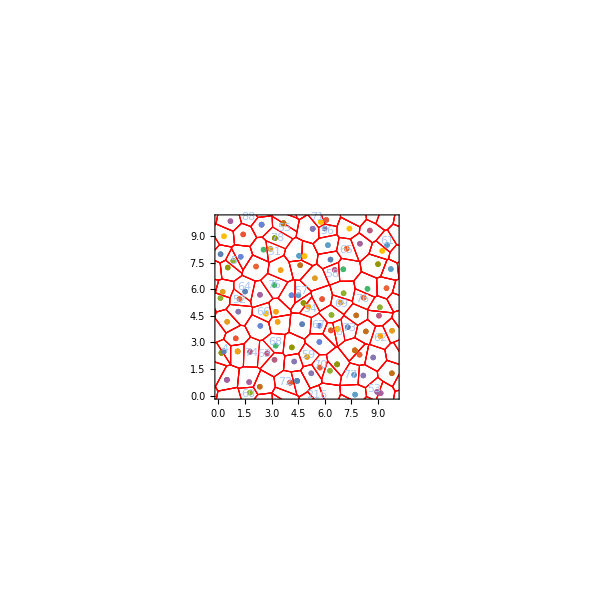

```mathematica
Show[HighlightMesh[vm,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dlwrong,dl,PlotRange->{{0,10},{0,10}},Frame->True]
```

### Case one: Two extremely close cells leads to false Voronoi tessellation

Most of the crazily high results are due to similar situations like this one.

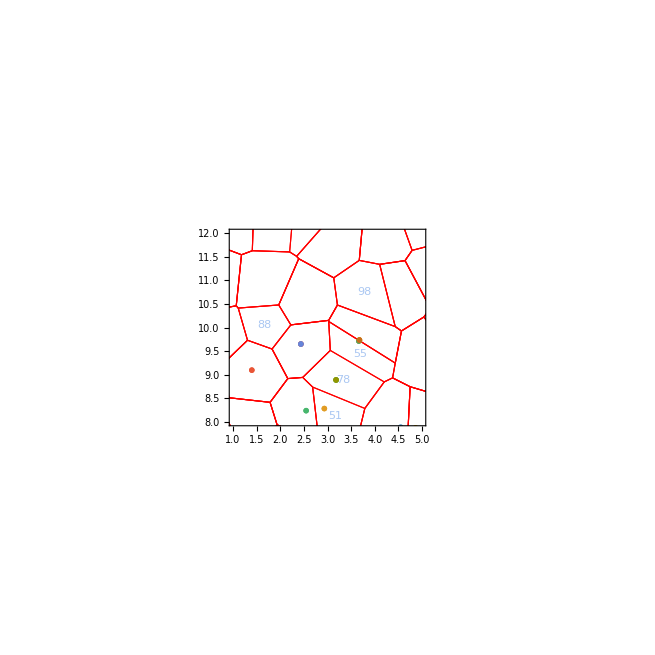

```mathematica
Show[HighlightMesh[vm,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dlwrong,dl,PlotRange->{{1,5},{8,12}},Frame->True]
```

```mathematica
(*The below is the neighbors of cell 100 from cellGPU. As you can see, in mathematica, 96 is not a neighbor of cell 100.*)
```

```mathematica
Normal[data[[4,1]]][[99*9+1;;100*9]]+1
```

{15,96,87,45,2,52,0,0,0}

```mathematica
(*If cellGPU were right, the circumcicle formed by cell 100, 15, 96 should be empty. However, this circumcircle is too larger and can never be empty.*)
```

```mathematica
circumcircle1=Circumsphere[{positions[[100]],positions[[15]],positions[[96]]}]
```

Sphere[{17.3016,1.19742},16.0793]

```mathematica
RegionMember[Disk[{17.30156448158344,1.1974226633073257},16.079329226371797],positions[[48]]]
```

True

### Case two: The existence of short edge leads to false Voronoi tessellation

Situations like this might not lead to a very large deviation between the Mathematica and cellGPU calculations.

```mathematica
(*The blue circle is circumcicle formed by cell 31, 73, 24*)
```

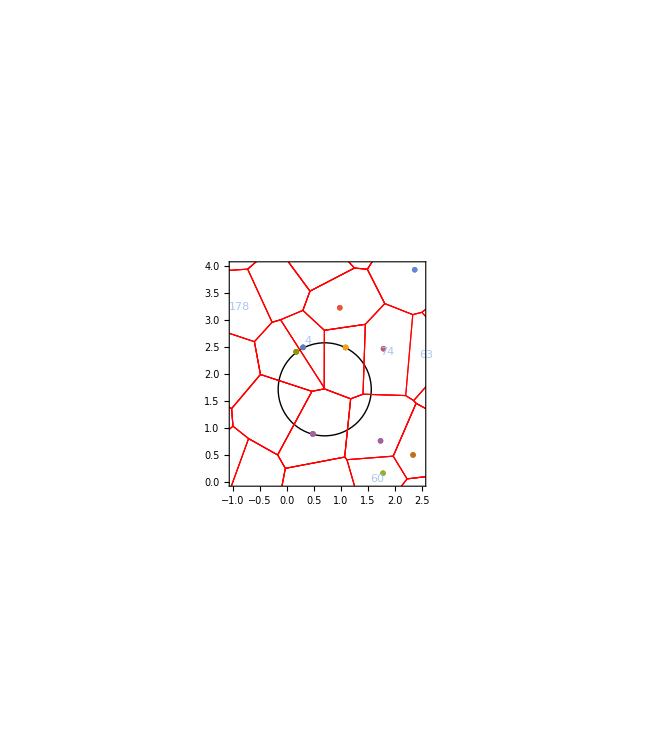

```mathematica
Show[HighlightMesh[vm,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],Graphics[circumcircle2],dlwrong,dl,PlotRange->{{-1,2.5},{0,4}},Frame->True]
```

```mathematica
(*The below is the neighbors of cell 24 from cellGPU. As you can see, in mathematica, 31 is not a neighbor of cell 24.*)
```

```mathematica
Normal[data[[4,1]]][[23*9+1;;24*9]]+1
```

{25,51,99,69,39,73,31,0,0}

```mathematica
(*If cellGPU were right, the circumcicle formed by cell 31, 73, 24 should be empty. However, cell 25 is inside this circumcircle.*)
```

```mathematica
circumcircle2=Circumsphere[{positions[[31]],positions[[73]],positions[[24]]}]
```

Sphere[{0.689168,1.72544},0.862276]

```mathematica
RegionMember[Disk[{0.6891675758983355,1.7254353753118865},0.8622758040809833],positions[[25]]]
```

True

```mathematica
(*If we zoom in and plot Delauney triangulation, it's more ovbious that cell 25 is inside the circumcircle.*)
```

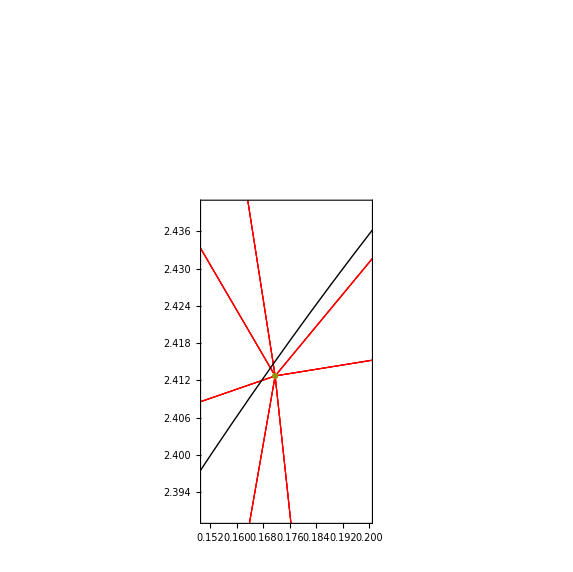

```mathematica
Show[HighlightMesh[dt,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],Graphics[circumcircle2],dlwrong,dl,PlotRange->{{0.15,0.2},{2.39,2.44}},Frame->True]
```

### Case three: The existence of short edge leads to false Voronoi tessellation

This is similar to case two.

```mathematica
(*The blue circle is circumcicle formed by cell 6, 10, 98*)
```

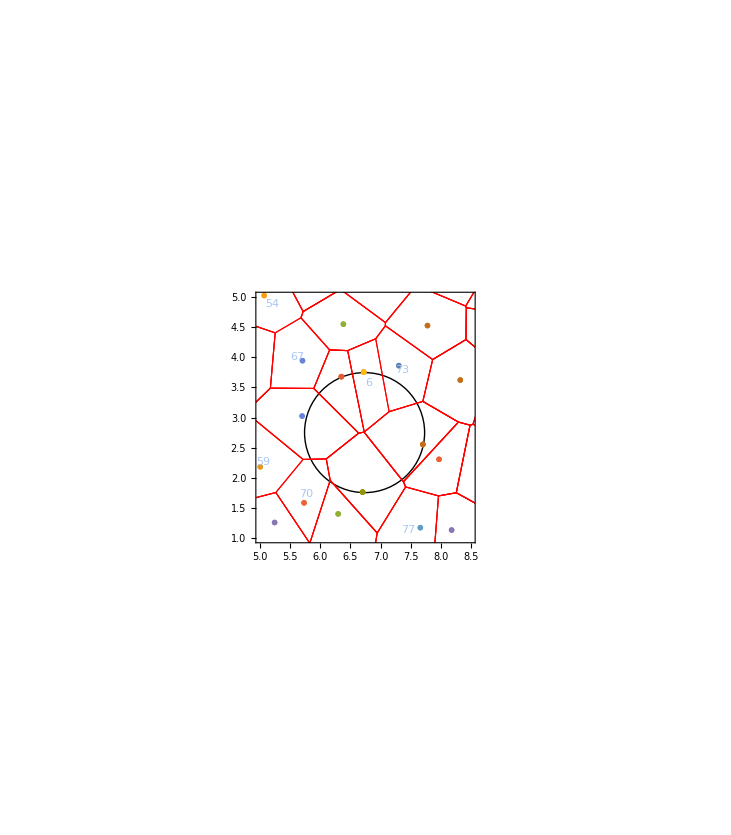

```mathematica
Show[HighlightMesh[vm,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],Graphics[circumcircle3],dlwrong,dl,PlotRange->{{5,8.5},{1,5}},Frame->True]
```

```mathematica
(*The below is the neighbors of cell 98 from cellGPU. As you can see, in mathematica, 10 is not a neighbor of cell 98.*)
```

```mathematica
Normal[data[[4,1]]][[97*9+1;;98*9]]+1
```

{76,18,41,10,6,0,0,0,0}

```mathematica
(*If cellGPU were right, the circumcicle formed by cell 98, 10, 6 should be empty. However, cell 41 is inside this circumcircle.*)
```

```mathematica
circumcircle3=Circumsphere[{positions[[98]],positions[[10]],positions[[6]]}]
```

Sphere[{6.72651,2.7573},0.996434]

```mathematica
RegionMember[Disk[{6.726506059247208,2.757301075099998},0.9964342818324575],positions[[41]]]
```

True

```mathematica
(*If we zoom in and plot Delauney triangulation, it's more ovbious that cell 25 is inside the circumcircle.*)
```

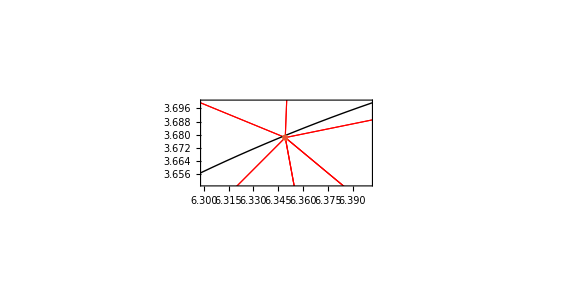

```mathematica
Show[HighlightMesh[dt,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],Graphics[circumcircle3],dlwrong,dl,PlotRange->{{6.3,6.4},{3.65,3.7}},Frame->True]
```